```mathematica
Today
```

Sun 29 Apr 2018

# Brainfilling Segments

Simple line segments can be used to draw arbitrarily complex things, but it is not always fun to stay within the lines. When drawing some graphical shape whose edge is a sequence of line segments, as long as each line segment starts and ends where it is supposed to, we can allow these line segments to meander in some controlled but more interesting way between these two points. The overall general shape of the image is still as it should be, but the resulting image will be much more interesting to look at. If this line segment is broken down into smaller line segments, we can continue this construction as deep as we want, at least until each piece is small enough that our eyes can no longer tell them apart.
“Brainfilling Curves: A Fractal Bestiary” by Jeffrey Ventrella, available to read for free on its home page, is an excellent introduction to the theory and practice of fractal subdivisions of line segments, and a nice catalogue to he subdivision rules that work well in practice to produce elegant results. These subdivision rules are chosen that the zaggy lines that they produce never intersect themselves. This restriction, of course, is not any kind of law of nature, but conforming to it makes the result look more elegant.
Cleverly chosen subdivision rules can furthermore guarantee that the fractal line segment sequence completely fills the two-dimensional area that bounds it, in the sense that a subdivision does not leave inside that area any holes larger than whatever ϵ > 0 you may freely choose to be as close to zero as you with, assuming that the subdivision is performed to the fixed finite depth d(ϵ) that depends on your chosen ϵ. The fractal dimension of this one-dimensional curve is therefore actually two! 
In the Mathematica code that we go through in this document, each recursive subdivision rule is defined as a list of smaller line segments that make up that subdivision. Each line segment in the subdivision is defined by four numerical parameters; its turn angle, its scaling factor compared to the length of the original line, the handedness of that segment (either +1 for left-handed or -1 for right-handed) and the direction of that segment (either +1 for forward or -1 for backward).
For example, a rule that defines the famous Koch curve subdivides each line segment into four pieces whose length is one third of the original line segment, using turns of exactly 60 degrees along the way to make room for the curve whose length is 4 / 3 of the original. Repetitions of this subdivision will then make the length of this curve approach infinity within a finite area, leaving less and less room for holes inside the bounding area since no points are ever visited twice.

```mathematica
τ = 2π;
koch = With[{s = τ/6, l = 1/2},{{0,1/3,+1,+1},{-s, 1/3,+1, +1}, {2s, 1/3,+1, +1}, {-s, 1/3,+1, +1}} ];
```

In all these formulas, you should note that the angles used in Mathematica trigonometric operations are measured in radians. Since there are 2π radians around the entire circle, a quantity usually denoted by the Greek letter τ (“tau”) that in practice ends up being used at least as often than its more famous cousin π, the angle τ / 6 = π / 3 corresponds to a 60 degree turn. A negative angle denotes a right turn, whereas a positive angle denotes a left turn. Because the subdivided path is supposed to finish heading in the exact same direction as the original line segment, the turn angles along the subdivision path should always add up to zero. This should be easy enough to verify.

```mathematica
Total[Map[First, koch]] == 0
```

True

The function to generate the subdivided points for the line segment subdivision using the given rule is best done with recursion. The function generatePoints receives as its arguments the rule to use to subdivide the line segment, followed by the starting point cp and direction vector dv that define the line segment under subdivision, followed by the sign of the handedness of the subdivision and the recursion depth. In the base case where depth equals zero, the result of subdividing the line segment consists of its start and end points. Otherwise, the subdivision path is constructed by joining the lists of paths generated by the individual steps of the subdivision rule.
The function pointBaseFunction that determines the result in the base case of the recursion is defined separately, so that we can later easily adjust the behaviour. Because the construction by concatenating subdivisions of the line segment duplicates the point that is simultaneously the endpoint of the previous subdivision and the starting point of the next subdivision, we define a utility function removeDuplicates to eliminate such duplications. This function can be defined in Mathematica as a one-liner with the aid of Split that creates a list of sublists of equal consecutive elements, and then mapping each sublist to its First element to drop the duplicates.

```mathematica
pointBaseFunction[sp_,dv_] := {sp,sp+dv};
removeDuplicates[list_] := Map[First, Split[list]];
generatePoints[rule_,sp_,dv_,sign_,depth_ /; depth < 1] := pointBaseFunction[sp,dv];
generatePoints[rule_,sp_, dv_, sign_,depth_] := Module[{pos, dir, result,turn,scale, handed, nrev, npos},
pos = sp;
dir = dv;
result = {};
Do[
{turn, scale,handed, nrev} =rule[[i]];
dir = With[{rot=RotationTransform[sign * turn ]},rot[dir]];
npos = pos +  scale * dir;
result = Join[result, 
If[nrev == +1, 
generatePoints[rule,pos, scale*dir, sign * handed,depth-1],
Reverse[generatePoints[rule,npos, -scale*dir, sign*handed, depth-1]]]
];
pos = npos,
{i,1,Length[rule]}];
removeDuplicates[result]
];
```

To create a shape known as Koch snowflake, the Koch curve subdivision is used to the line segments of an equilateral hexagon. The utility function polygonPoint computes the coordinates of the i:th point of the regular n-sided polygon that is centered at the origin. Each line segment then starts at the i:th corner and has the direction vector that connects it to the next corner i + 1. (Since the sine and cosine functions are periodic, the n:th corner of the polygon loops back to the zeroth corner.) The following image shows the Koch snowflakes with the recursion depth from 0 to 5, rendered from the inside out.

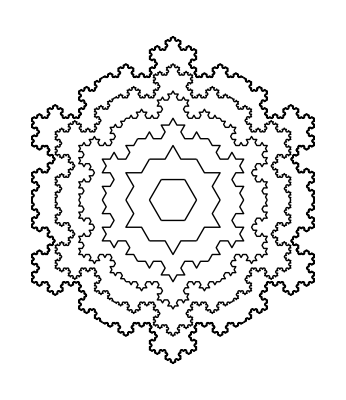

```mathematica
polygonPoint[i_,n_] := {Cos[i * τ/n],Sin[i * τ/n]};
Graphics[Table[With[{r = .5+.5d},Line[generatePoints[koch, r polygonPoint[i,6],r polygonPoint[i+1,6]-r polygonPoint[i,6],+1,d]]],{i,0,5},{d,0,5}]]
```

Sierpinski triangle is another famous fractal that tends to pop up in surprising places. The triangle is usually defined using a planar subdivision of a triangle, but its outline can be defined as a subdivision curve.

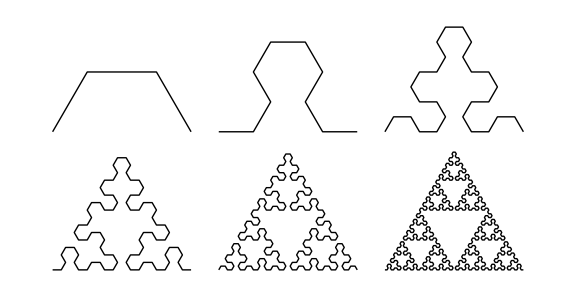

```mathematica
pointBaseFunction[sp_,dv_] := {sp,sp+dv};
sierpinskiOutline = With[{s = τ/6},
{{s,1/2,-1,+1},{-s,1/2,+1,+1},{-s,1/2,-1,+1},{s,0,-1,+1}}
];
Graphics[{
Table[Line[generatePoints[sierpinskiOutline,{1.2Mod[d-1,3],1-Floor[(d-1)/3]},{1,0},+1,d]],{d,1,6}]
}, ImageSize -> Large]
```

In this subdivision, it is quite important that the first and last line segments are right-handed and the middle segment is left-handed. Flipping the handedless makes the line segments bulge outwards instead of filling the insides of the surrounded triangle, resulting in a bit different fractal shape.

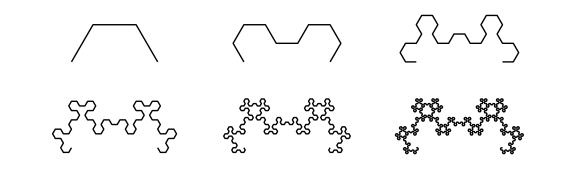

```mathematica
sierpinskiFlipped = With[{s = τ/6},
{{s,1/2,+1,+1},{-s,1/2,-1,+1},{-s,1/2,+1,+1},{s,0,-1,+1}}
];
Graphics[{
Table[Line[generatePoints[sierpinskiFlipped,{2Mod[d-1,3],1-Floor[(d-1)/3]},{1,0},+1,d]],{d,1,6}]
}, ImageSize -> Large]
```

The next subdivision rule produces a variation of the Gosper curve. We need to adjust the pointBaseFunction to return only the starting point of the atomic line segment, which prevents the points of the curve touching the line segments later in the curve, when this sequence of points is rendered as a single smooth B-spline instead of sequential line segments. To speed up the computation, we use only the approximate floating point numbers given by Mathematica function N to compute the coordinates instead of the exact symbolic solutions. Our eyes could not possibly tell the difference anyway in the screen or even the print resolution.

```mathematica
gosper = With[{tk = N[τ/3], sc = N[2.2/Sqrt[34]]},
{{-ArcTan[Sqrt[3]/5],0,+1,+1},{0,sc,+1,+1},{0,sc,+1,-1},{tk,sc,+1,-1},{tk,sc,+1,-1},{-tk,sc,+1,+1},
{-tk,sc, +1,+1},{0,sc,+1,+1}}
];
pointBaseFunction[sp_,dv_] := {sp };
Graphics[BSplineCurve[generatePoints[gosper,{0,0},{1,0},-1,4]], ImageSize -> Large]
```

-Graphics-

Variations of Gosper curve and the related Dragon curve are even more elegant in that not only do they completely fill in the area that they cover, but they can be used to to tile the plane by placing them side by side like pieces of a jigsaw puizzle. For example, using three copies of the Gosper curve to subdivide the three line segments that make up an equilateral triangle, and this time filling in the internal area that this curve encloses instead of just drawing this boundary line, produces a rather pretty hexagonal fractal shape.

```mathematica
gpts := 
removeDuplicates[Flatten[Join[Table[generatePoints[gosper,polygonPoint[i,3],polygonPoint[i+1,3]-polygonPoint[i,3], +1,3],{i,0,2}]],1]];
Graphics[FilledCurve[BSplineCurve[gpts, SplineDegree -> 4,SplineClosed -> True]], ImageSize -> Large]
```

-Graphics-

A similar rule that uses two different turn angles along the way produces another, equally elegant shape that also meshes perfectly together with itself when used to subdivide the line segments of an equilateral hexagon. Before drawing the B-spline curve, each point is transformed using a perspective projection based on a distance function that increases when moving away from the origin.

```mathematica
pointBaseFunction[sp_,dv_] := {sp };
gosper2 = With[{tk = N[τ/3], s = N[2π/6],sc =2.2/Sqrt[34]},
{{-ArcTan[Sqrt[3]/5],0,+1,+1},{s,sc,+1,+1},{s,sc,+1,+1},{-tk,sc,+1,+1},{-tk,sc,+1,+1},{s,sc,+1,+1},{s,sc,+1,+1},{s,sc,+1,+1}
}];
gpts2 := 
removeDuplicates[Flatten[Join[Table[generatePoints[gosper2,polygonPoint[i,6],polygonPoint[i+1,6]-polygonPoint[i,6], +1,3],{i,0,5}]],1]];
project[{x_,y_}] := With[{z = 1.5Sin[-.17x+.89y]+1.3Cos[.67x-.55y] +2EuclideanDistance[{x,y},{0,0}]},
{x/(4+z), y/(4+z)}
];
Graphics[{EdgeForm[{Thick,Black}],Green, FilledCurve[BSplineCurve[Map[project,gpts2], SplineClosed -> True, SplineDegree -> 3]]}, ImageSize -> Large]
```

-Graphics-

There is no law of nature saying that the consecutive points have to be connected by line segments. For artistic purposes, we can do whatever we want with the sequence of points generated by the subdivision process. The next example of a simple subdivision rule partitions the generated sequence of points into triangles, which it then renders using different colours.

```mathematica
pointBaseFunction[sp_,dv_] := {sp +dv/2};
rule = With[{f = τ/4},{{-f, 1/2,-1, -1}, {+f, 1/2,+1, +1}, {+f, 1/2,+1, -1}, {-f, 1/2,+1, +1}}];
flip[{dx_,dy_}] := {-dy, dx};
perturb[{x_,y_},sc_] := {x,y} +RandomVariate[NormalDistribution[0,sc],2]
shape[pts_,cf_] := With[{p1 =pts[[1]],p2=pts[[2]]},
With[{d = 0.04ManhattanDistance[p1,p2]},
With[{q1 = perturb[p1,d], q2 = perturb[p2,d]},{cf[RandomReal[{.1,.9}]],Polygon[{q1,q2,q2 + .9flip[q2-q1]}]}]]];
ImageDeconvolve[ImageEffect[Image[Graphics[{EdgeForm[],Table[Table[shape[pts,cf],{pts, Partition[generatePoints[rule,{0,0},{1,0},+1,3],2,1]}],{cf,Map[ColorData,{"SouthwestColors","SunsetColors","AuroraColors"}]}]}, Background ->White, ImageSize -> 600
]
], {"PoissonNoise",.05}],
{{.25,.5,-.25},{-.5,-.5,.5},{.25,.5,.25}}
]
```

-Graphics-

Of the previous subdivision rules, only the Gosper curve used line segments that were reversed, so let’s rectify this. Our final shape is nameless, taken from page 155 of “Brainfilling Curves”, contains both left- and right-handed segments going forward and backward to carefully avoid intersecting itself. This fractal is not space-filling, but still interesting in its way to look at.

```mathematica
bfc155 = With[{f = τ/4},{
{f,1/2,-1,-1},{-f,1/3,-1,+1},{0,1/3,+1,+1},{0,1/3,+1,-1},{-f,1/2,-1,-1},{f,0,+1,+1}
}];
Graphics[{Thick,BSplineCurve[generatePoints[bfc155,{0,0},{1,0},+1,5], SplineDegree -> 2]}, ImageSize -> Large]
```

-Graphics-

Now take the the points from this curve, generated up to depth of four, and render these points as curves going through five randomly chosen points within the same block of five consecutive points.

```mathematica
shape[pts_,cf_] := 
{cf[RandomReal[]],BSplineCurve[pts[[Sort[RandomSample[Range[1,Length[pts]],5]]]]]};
strands =Image[With[{cfs = Map[ColorData,{"Rainbow", "WatermelonColors", "SolarColors"}], pointlist = generatePoints[bfc155,{0,0},{1,0},+1,4]},Graphics[{Thickness[.01],
Table[shape[pts,RandomChoice[cfs]],{pts,RandomSample[Partition[pointlist,40,4]]},{i,1,3}]
}, ImageSize -> Large]]];
Blend[{
strands,
GeometricMeanFilter[strands,1],
ImageDeconvolve[strands, DiskMatrix[3]/Total[DiskMatrix[3],{2}]]
},{2,-1,1}]
```

-Graphics-